```mathematica
ClearAll["Global`*"]
```

```mathematica
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.csv"],Transpose@{
(Transpose@mydata["BackgroundFields"])[[1]],
(Transpose@mydata["BackgroundFields"])[[2]],
mydata["Alpha"],(*dimensionless*)
mydata["Time"],(*in fm/c*)
mydata["Radius"],(*in fm*)
mydata["TimeDerivative"],(*in fm/c*)
mydata["RadialDerivative"](*in fm*)
},"CSV"];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.txt"],{{1,2,3},{10,20,30}},"List"];
```

```mathematica
Keys[mydata]
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

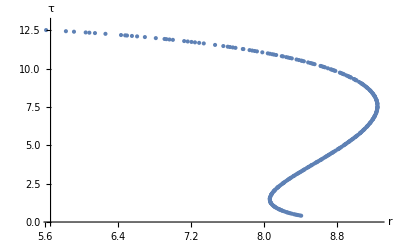

```mathematica
FreezeOutPlot=ListPlot[Transpose[{mydata["Radius"],mydata["Time"]}],AxesLabel->{r,τ}]
```

```mathematica
dalpha=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
ur=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]][[1;;-2]]]]; (*dimensionless*)
utau=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]][[1;;-2]]]]; (*dimensionless*)
```

```mathematica
Solve[a==(x+b)*(3*x-b)/(2*c),x]
```

{{x→1/3 (-b-√2 √(2 b^2+3 a c))},{x→1/3 (-b+√2 √(2 b^2+3 a c))}}

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
mσ=0.6;(*mass of the sigma field ~ 400-800 MeV in GeV*)
ϵ=0.01*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
vev=0.15;(*??? vev of sigma field ??? pion decay constant ???, in GeV*)
χ2=(-mσ^2+2*mσ*Sqrt[3*ϵ*(IfmtoGeV^3)/vev^2+mσ^2])/6;(*in GeV^2*)
χ=Sqrt[χ2];(*in GeV*)
(*θ0=0.5; This will be taken care of later*)

θ=χ*Accumulate[(mydata["TimeDerivative"][[1;;-2]]*utau-mydata["RadialDerivative"][[1;;-2]]*ur)*fmtoIGeV*dalpha];(*dimensionless*)
ρ=Sqrt[vev*(2*χ2+mσ^2)/(mσ^2)];(*in GeV*)
ϕfreeze=ρ*Exp[I*θ];(*in GeV*)
π0=Sqrt[2]*Im[ϕfreeze];(*in GeV*)
σ0=Sqrt[2]*Re[ϕfreeze];(*in GeV*)
ThetaPlot=ListPlot[θ,AxesLabel->{None,"θ"}];
```

```mathematica
Integrate[Exp[I*(a*Cos[x])],{x,0,2*Pi},Assumptions->Element[a,Reals]]
```

2 π BesselJ[0,Abs[a]]

```mathematica
rs=mydata["Radius"][[1;;-2]];
drs=mydata["RadialDerivative"][[1;;-2]];
taus=mydata["Time"][[1;;-2]];
dtaus=mydata["TimeDerivative"][[1;;-2]];
```

```mathematica
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[p_]=BesselJ[0,rs*p*GeVtoIfm];(*dimensionless*)
J1rp[p_]=BesselJ[1,rs*p*GeVtoIfm];(*dimensionless*)
Y0tw[p_]=BesselY[0,taus*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[p_]=BesselY[1,taus*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[p_]=BesselJ[0,taus*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[p_]=BesselJ[1,taus*ω[p]*GeVtoIfm];(*dimensionless*)

H1[p_]=J0rp[p]*(-Y0tw[p]+I*J0tw[p]);(*dimensionless*)
H2[p_]=dtaus*fmtoIGeV*p*J1rp[p]*(-Y0tw[p]+I*J0tw[p])+(*dimensionless*)
drs*fmtoIGeV*J0rp[p]*ω[p]*(-Y1tw[p]+I*J1tw[p]);(*dimensionless*)
```

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
ps=logspace[-3,0.5,100];(*in GeV*)
ps=linspace[0,2,100];
Print[Min[ps]," to ",Max[ps], " GeV"]
```

0 to 2 GeV

```mathematica
(*σ0=σfreeze*Cos[θ0]-πfreeze*Sin[θ0]
π0=πfreeze*Cos[θ0]+σfreeze*Sin[θ0]*)
H1ps=H1[ps];
H2ps=H2[ps];

(*The C's all have dimension IGeV*)
C1σ=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*((-1)*π0*χ*(-drs*utau+dtaus*ur)*H1ps)];(*I guess u_tau=-u^tau*)
C1π=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*(σ0*χ*(-drs*utau+dtaus*ur)*H1ps)];
C2σ=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*σ0*H2ps];
C2π=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*π0*H2ps];

Jps[θ0_]=(C1σ+C2σ)*Sin[θ0]+(C1π+C2π)*Cos[θ0];
```

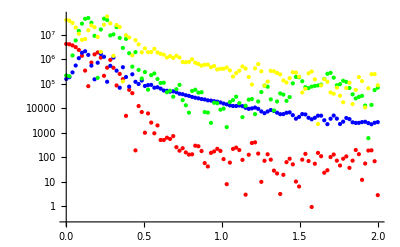

```mathematica
ListLogPlot[
{Transpose@{ps,Abs[C1σ]^2},
Transpose@{ps,Abs[C1π]^2},
Transpose@{ps,Abs[C2σ]^2},
Transpose@{ps,Abs[C2π]^2}},
PlotStyle->
{Directive[Red,PointSize[Medium]],
Directive[Blue,PointSize[Medium]],
Directive[Green,PointSize[Medium]],
Directive[Yellow,PointSize[Medium]]}
]
```

```mathematica
Manipulate[
ListLogPlot[Transpose@{ps,Abs[Jps[θ0]]^2},AxesLabel->{"p [GeV]","|π(p)|^2"}]
,{θ0,0,2*Pi}]
```

```mathematica
Alicedatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*Alicedata=ImportString[StringReplace[StringReplace[Alicedatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
Alicedata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[Alicedata];
titles=Alicedata[[1]]
πplus=Alicedata[[2;;42]];
πminus=Alicedata[[44;;]];
aliceps=(Transpose@πplus)[[1]];
aliceyieldplus=(Transpose@πplus)[[4]];
aliceyieldminus=(Transpose@πminus)[[4]];
```

{PT [GEV],PT [GEV] LOW,PT [GEV] HIGH,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2],stat +,stat -,sys +,sys -,sys,normalization uncertainty +,sys,normalization uncertainty -}

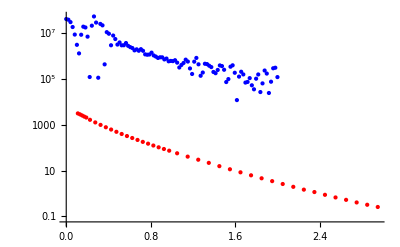

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListNumeric=Transpose@{ps,Abs[Jps[0]]^2};
ListLogPlot[
{ListALICE,ListNumeric},
PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]}
]
```

```mathematica
Manipulate[
ListLogPlot[
{ListALICE,Transpose@{ps,(10^-4)*Abs[Jps[θ0]]^2}},
PlotStyle->{Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]}
]
,{θ0,0,2*Pi}
]
```